```mathematica
J=12;
L=20;
```

```mathematica
P[a3_,a2_,a1_,a0_]:=a3 f^3+a2 f^2+a1 f+a0
```

```mathematica
p=(3 a1 a3-a2^2)/(3 a3^2);
q=(2 a2^3-9a1 a2 a3+27a0 a3^2)/(27 a3^3);
```

```mathematica
solutions=Table[Subscript[f, k]->-a2/(3a3)+2 √(-p/3)Cos[1/3 ArcCos[(3q)/(2p)√(-3/p)]+(2π k)/3],{k,1,3}]/.{a3->1,a2->J,a1->L,a0->ξ}
```

{f_1→-4-4 √(7/3) Sin[π/6+1/3 ArcCos[-(1296+27 ξ)/(336 √21)]],f_2→-4-4 √(7/3) Sin[π/6-1/3 ArcCos[-(1296+27 ξ)/(336 √21)]],f_3→-4+4 √(7/3) Cos[1/3 ArcCos[-(1296+27 ξ)/(336 √21)]]}

```mathematica
I3=(Subscript[f, 3]-Subscript[f, 1])/(Subscript[f, 3]-Subscript[f, 2])/.solutions;
```

```mathematica
DI3=D[I3,ξ]//Simplify
```

(3 Sec[1/6 (π+2 ArcCos[-3/112 √(3/7) (48+ξ)])]^2)/(2 √(25600-2592 ξ-27 ξ^2))

```mathematica
NSolve[Denominator[DI3]==0,ξ]
```

{{ξ→-105.028},{ξ→9.02761}}

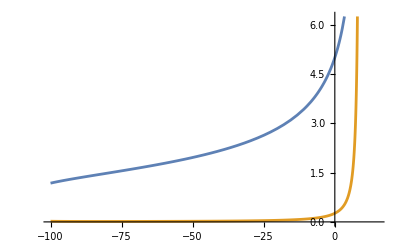

```mathematica
Plot[{I3,DI3},{ξ,-100,15}]
```